Your Title Here

```mathematica
(*p1=Graphics[{
{EdgeForm[],GrayLevel[0.6],
FilledCurve[{
{BezierCurve[{{0,3},{1,4},{2,4},{3,3}}],
Line[{{3,3},{3,0}}]},
{BezierCurve[{{0,0},{1,-1},{2,-1},{3,0}}],
Line[{{0,3},{0,0}}]}}]},
{Thick,BezierCurve[{{0,3},{1,4},{2,4},{3,3}}],BezierCurve[{{0,0},{1,-1},{2,-1},{3,0}}],Line[{{3,3},{3,0}}],Line[{{0,3},{0,0}}]},
{Thick,Arrowheads[0.075],
Arrow[{{-1.25,1.5},{0,1.5}}],
Arrow[{{1.5,3.75},{1.5,4.75},{3.75,4.75}}],
Arrow[{{1.5,-0.75},{1.5,-1.75},{3.75,-1.75}}]},

Text[Style["feed",17],{-1,2}],
Text[Style["vapor",17],{2.625,4.75},{0,-1}]
}];*)
```

```mathematica
Manipulate[
Module[{δx,x1,x2,x3,x4,y1,y2,y3,δy,h,xf,p1,δdome,f},
(*COLUMN*)
δx=1;
x1=0;x2=x1+δx;x3=x2+δx;x4=x3+δx;
δy=1;h=3;
y1=δy;
y2=y1+h;
y3=y2+δy;

(*ARROWS*)
xf=x1-1.25;
f=BezierFunction[{{x1,y1},{x2,0},{x3,0},{x4,y1}}];

(*p1=Graphics[{
Line[{Table[{x,-0.5*√(1-x^2)+y1},{x,x1,x4}]}],
(*{EdgeForm[],GrayLevel[0.6],
FilledCurve[{
{(*BezierCurve[{{x1,y1},{x2,0},{x3,0},{x4,y1}}],*)
Interpolation[Table[{x,-0.5*√(1-x^2)+y1},{x,x1,x4}]],
Line[{{x4,y1},{x4,y2}}]},
{BezierCurve[{{x1,y2},{x2,y3},{x3,y3},{x4,y2}}],
Line[{{x1,y1},{x1,y2}}]}
}]
},*)
{Thick,(*BezierCurve[{{x1,y1},{x2,0},{x3,0},{x4,y1}}],BezierCurve[{{x1,y2},{x2,y3},{x3,y3},{x4,y2}}],*)Line[{{x1,y1},{x1,y2}}],Line[{{x4,y1},{x4,y2}}]},
{Thick,Arrowheads[0.075],
Arrow[{{xf,y1+h/2},{x1,y1+h/2}}](*,
Arrow[{{(x1+x4)/2,*)
},
Text[Style["feed",17],{xf,y1+h/2},{0,-1}],


(*{Thick,Arrowheads[0.075],
Arrow[{{-1.25,1.5},{0,1.5}}],
Arrow[{{1.5,3.75},{1.5,4.75},{3.75,4.75}}],
Arrow[{{1.5,-0.75},{1.5,-1.75},{3.75,-1.75}}]},

Text[Style["feed",17],{-1,2}],
Text[Style["vapor",17],{2.625,4.75},{0,-1}]*)
}];

Show[p1,ImageSize->{500,430}]*)

(*Graphics[Line[Table[{x,-0.5*√(x4^2-x^2)+y1},{x,x1,x4}]]]*)

p1=Graphics[{
Line[Table[{x,0.5*Sin[x]+y2},{x,x1,x4,0.1}]],
Line[{{x1,y1},{x1,y2}}],Line[{{x4,y1},{x4,y2}}]
},Axes->True]

],
Control[{{cs,2,""},{1->" p1 ",2->" p2 "},Setter}]
]
```

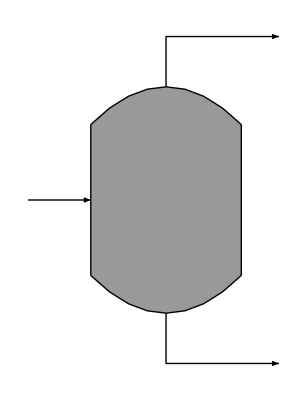
```mathematica
ImageDimensions[-Graphics-]
```

{336,432}

2.625





```mathematica
(1.5+3.75)/2
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX